# WaveSight - Calcs

Fiber optics gleam,
Bessel functions guide their beam,
Now take me yonder.

## Poynting Vector

```mathematica
(*in cartesian coordinates*)
ihat={1,0,0};
jhat={0,1,0};
khat={0,0,1};
gradTEz=D[Ez[x,y],x]*ihat+D[Ez[x,y],y]*jhat;
gradTHz=D[Hz[x,y],x]*ihat+D[Hz[x,y],y]*jhat;
Et=1/γ^2(kz gradTEz-ω μ0 Cross[khat, gradTHz]);
Ht=1/γ^2(kz gradTHz+ω ϵ0 n^2 Cross[khat, gradTEz]);
Exyz={Et[[1]],Et[[2]],Ez[x,y]};
Hxyz={Ht[[1]],Ht[[2]],Hz[x,y]};
(*...*)
```

```mathematica
(*in cylindrical coordinates*)
ρhat={1,0,0};
ϕhat={0,1,0};
zhat={0,0,1};
gradTEz=D[Ez[ρ],ρ]*ρhat+(I m)/ρ Ez[ρ]*ϕhat;
gradTHz=D[Hz[ρ],ρ]*ρhat+(I m)/ρ Hz[ρ]*ϕhat;
Et=I/γ^2(kz gradTEz-ω μ0 Cross[zhat, gradTHz]);
Ht=I/γ^2(kz gradTHz+ω ϵ0 n^2 Cross[zhat, gradTEz]);
Eρϕz={Et[[1]],Et[[2]],Ez[ρ]Exp[I m ϕ]};
Hρϕz={Ht[[1]],Ht[[2]],Hz[ρ]Exp[I m ϕ]};
Hρϕz=Hρϕz/.{I->-I};
S=Simplify[Cross[Eρϕz,Hρϕz]];
S=Re[S];
S=S/.{Ez[ρ]->Ez, Ez'[ρ]->Ezp,Hz[ρ]->Hz, Hz'[ρ]->Hzp};
S=1/2 FullSimplify[ComplexExpand[S],Assumptions->{
ρ>0,ϕ>0,
ϵ0>0,μ0>0,n>1,
Element[m,Integers],Element[γ,Reals],
Element[Hz,Reals],Element[Hzp,Reals],
Element[Ez,Reals],Element[Ezp,Reals],
Element[kz,Reals]1}];
(*...*)
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
Needs["MaTeX`"]
```

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k^2} = \\frac{\\pi^2}{6}",FontSize->24]
```

-Graphics-

```mathematica
final=StringReplace[ToString[TeXForm[S]],{
"\\text{kz}"->"k_z",
"\\text{Ez}"->"E_z",
"\\text{Ezp}"->"\\frac{\\partial E_z}{\\partial \\rho}",
"\\text{Hz}"->"H_z",
"\\text{Hzp}"->"\\frac{\\partial H_z}{\\partial \\rho}",
"\\text{$\\epsilon $0}"->"\\epsilon_0 ",
"\\text{$\\mu $0}"->"\\mu_0 "
}];
CopyToClipboard[final];
MaTeX[final]
```

-Graphics-

```mathematica
FullSimplify[Re[ComplexExpand[ⅇ^(-ⅈ m ϕ)/(γ^2 ρ)(Ez Hz kz m-I) ]],Assumptions->{m>0,ϕ>0,γ>0,ρ>0,Element[Ez,Reals],Element[kz,Reals],Element[Hz,Reals]}]
```

(Ez Hz kz m Cos[m ϕ]-Sin[m ϕ])/(γ^2 ρ)

```mathematica
Eρϕz
```

{(ⅈ ((ⅈ m μ0 ω Hz[ρ])/ρ+kz Ez'[ρ]))/γ^2,(ⅈ ((ⅈ kz m Ez[ρ])/ρ-μ0 ω Hz'[ρ]))/γ^2,ⅇ^(ⅈ m ϕ) Ez[ρ]}

```mathematica
gradTEz
```

{Ez^(1,0)[ρ,ϕ],Ez^(0,1)[ρ,ϕ],0}

```mathematica
{kix,kiy,  √(nf^2/ni^2(kix^2+kiy^2+kiz^2) -(kix^2+kiy^2))}
```

{kix,kiy,√(-kix^2-kiy^2+((kix^2+kiy^2+kiz^2) nf^2)/ni^2)}

```mathematica
(*incident wave vector*)
kvec={kx,ky,kz};
(*its magnitude*)
k=ω √(μ ϵ);

(*refraction wave vector*)
kpvec={kx,ky,√(ω^2 ϵp μp -kx^2-ky^2)};
(*Its magnitude*)
kp=ω √(μp ϵp);

(*reflected wave vector*)
kppvec={kx,ky,-kz};
(*mag same as incident*)
kpp=k;

(*Incident electric field*)
E0={E0x,E0y,E0z};
(*Refracted electric field*)
Ep={Epx,Epy,Epz};
(*Reflected electric field*)
E0pp={E0ppx,E0ppy,E0ppz};
(*Incident H-field*)
H0=(√(μ ϵ))/μ Cross[kvec,E0]/k;
(*Refracted H field*)
Hp=(√(μp ϵp))/μp Cross[kpvec,Ep]/kp;
(*Reflected H field*)
H0pp=(√(μ ϵ))/μ Cross[kppvec,E0pp]/kpp;

nhat={0,0,1};
eq1=ϵ(E0+E0pp).nhat-ϵp Ep.nhat;
eq2=1/μp(H0+H0pp).nhat-1/μ Hp.nhat;
eq3=Cross[(E0+E0pp),nhat]-Cross[ Ep,nhat];
eq4=Cross[(H0+H0pp),nhat]-Cross[ Hp,nhat];
eqns=Flatten[{eq1,eq2,eq3,eq4}];
eqns=Simplify[eqns];
eqns=Select[eqns,Not[#===0]&];
eqns=Simplify[eqns];
(*eqns=eqns/.{kx->0,μ->1,μp->1,E0z->0,E0y->0,E0ppz->0,E0ppy->0,Epz->0,Epy->0};*)
eqns=Select[eqns,Not[#===0]&];
eqns=Simplify[(#==0)&/@eqns,Assumptions->{μ>0,μp>0,ω>0}];
```

```mathematica
eqns
```

{(E0ppz+E0z) ϵ-Epz ϵp,(E0ppy kx+E0y kx-Epy kx-E0ppx ky-E0x ky+Epx ky)/(μ μp ω),E0ppy+E0y-Epy,-E0ppx-E0x+Epx,-(-Epz kx μ+E0ppz kx μp+E0z kx μp+E0ppx kz μp-E0x kz μp+Epx μ √(-kx^2-ky^2+ϵp μp ω^2))/(μ μp ω),-(-Epz ky μ+E0ppz ky μp+E0z ky μp+E0ppy kz μp-E0y kz μp+Epy μ √(-kx^2-ky^2+ϵp μp ω^2))/(μ μp ω)}

```mathematica
psol=Solve[eqns,{Epx,Epy,Epz,E0ppx,E0ppy,E0ppz}][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{Epy→(Epx ky)/kx+(2 (E0y kx-E0x ky) kz μp)/(kx (kz μp+μ √(-kx^2-ky^2+ϵp μp ω^2))),Epz→-(2 E0x kz ϵ μp)/(kx (ϵ μ-ϵp μp))-(Epx (-kz ϵ μp-ϵ μ √(-kx^2-ky^2+ϵp μp ω^2)))/(kx (ϵ μ-ϵp μp)),E0ppx→-E0x+Epx,E0ppy→(Epx ky)/kx-(-E0y kx kz μp+2 E0x ky kz μp+E0y kx μ √(-kx^2-ky^2+ϵp μp ω^2))/(kx (kz μp+μ √(-kx^2-ky^2+ϵp μp ω^2))),E0ppz→-(-E0z kx ϵ μ+E0z kx ϵp μp-2 E0x kz ϵp μp)/(kx (-ϵ μ+ϵp μp))-(Epx ϵp (kz μp+μ √(-kx^2-ky^2+ϵp μp ω^2)))/(kx (-ϵ μ+ϵp μp))}

```mathematica
psol/.{Epx->0}
```

{Epy→(2 (E0y kx-E0x ky) kz μp)/(kx (kz μp+μ √(-kx^2-ky^2+ϵp μp ω^2))),Epz→-(2 E0x kz ϵ μp)/(kx (ϵ μ-ϵp μp)),E0ppx→-E0x,E0ppy→-(-E0y kx kz μp+2 E0x ky kz μp+E0y kx μ √(-kx^2-ky^2+ϵp μp ω^2))/(kx (kz μp+μ √(-kx^2-ky^2+ϵp μp ω^2))),E0ppz→-(-E0z kx ϵ μ+E0z kx ϵp μp-2 E0x kz ϵp μp)/(kx (-ϵ μ+ϵp μp))}

```mathematica
eqns
```

{(-E0ppx ky-E0x ky+Epx ky)/ω,-E0ppx-E0x+Epx,-(E0ppx kz-E0x kz+Epx √(-ky^2+ϵp ω^2))/ω}

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
Epx/.psol
```

(2 E0x kz)/(kz+√(-ky^2+ϵp ω^2))

```mathematica
eqns/.{Epz->E0ppz+E0z}
```

{-(E0ppz kx+E0z kx-(E0ppz+E0z) kx)/ω,0,(E0ppz ky+E0z ky-(E0ppz+E0z) ky)/ω}

```mathematica
vars=Variables@Level[eqns,{-1}];
allVars={E0ppx,E0ppy,E0ppz,E0x,E0y,E0z,Epx,Epy,Epz,kx,ky,kz};
matForm=Coefficient[#,allVars]&/@eqns;
```

```mathematica
matForm//MatrixForm
```

(0 | 0 | ϵ | 0 | 0 | ϵ | 0 | 0 | -ϵp | 0 | 0 | 0
-ky/(μ μp ω) | kx/(μ μp ω) | 0 | -ky/(μ μp ω) | kx/(μ μp ω) | 0 | ky/(μ μp ω) | -kx/(μ μp ω) | 0 | (E0ppy+E0y-Epy)/(μ μp ω) | (-E0ppx-E0x+Epx)/(μ μp ω) | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-kz/(μ ω) | 0 | -kx/(μ ω) | kz/(μ ω) | 0 | -kx/(μ ω) | -(√(-kx^2-ky^2+ϵp μp ω^2))/(μp ω) | 0 | kx/(μp ω) | -E0ppz/(μ ω)-E0z/(μ ω)+Epz/(μp ω) | 0 | -(E0ppx μp-E0x μp)/(μ μp ω)
0 | -kz/(μ ω) | -ky/(μ ω) | 0 | kz/(μ ω) | -ky/(μ ω) | 0 | -(√(-kx^2-ky^2+ϵp μp ω^2))/(μp ω) | ky/(μp ω) | 0 | -E0ppz/(μ ω)-E0z/(μ ω)+Epz/(μp ω) | -(E0ppy μp-E0y μp)/(μ μp ω))

```mathematica
Coefficient[eqns[[1]],allVars]
```

{0,0,ϵ,0,0,ϵ,0,0,-ϵp,0,0,0}

```mathematica
eqns[[1]]
```

(E0ppz+E0z) ϵ-Epz ϵp

```mathematica
CoefficientList[2+x,{x}]
```

{2,1}

```mathematica
MatrixForm[matForm]
```

(0 | 0 | ϵ | 0 | 0 | ϵ | 0 | 0 | -ϵp | 0 | 0 | 0
-ky/(μ μp ω) | kx/(μ μp ω) | 0 | -ky/(μ μp ω) | kx/(μ μp ω) | 0 | ky/(μ μp ω) | -kx/(μ μp ω) | 0 | (E0ppy+E0y-Epy)/(μ μp ω) | (-E0ppx-E0x+Epx)/(μ μp ω) | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-kz/(μ ω) | 0 | -kx/(μ ω) | kz/(μ ω) | 0 | -kx/(μ ω) | -(√(-kx^2-ky^2+ϵp μp ω^2))/(μp ω) | 0 | kx/(μp ω) | -E0ppz/(μ ω)-E0z/(μ ω)+Epz/(μp ω) | 0 | -(E0ppx μp-E0x μp)/(μ μp ω)
0 | -kz/(μ ω) | -ky/(μ ω) | 0 | kz/(μ ω) | -ky/(μ ω) | 0 | -(√(-kx^2-ky^2+ϵp μp ω^2))/(μp ω) | ky/(μp ω) | 0 | -E0ppz/(μ ω)-E0z/(μ ω)+Epz/(μp ω) | -(E0ppy μp-E0y μp)/(μ μp ω))

```mathematica
solveVars={Epx,Epy,Epz,E0ppx,E0ppy,E0ppz};
inputVars={E0x,E0y,E0z}
matForm=Coefficient[#,solveVars]&/@eqns;
```

{E0x,E0y,E0z}

```mathematica
matForm=Coefficient[#,inputVars]&/@eqns;
```

```mathematica
MatrixForm[matForm]
```

(0 | 0 | ϵ
-ky/(μ μp ω) | kx/(μ μp ω) | 0
0 | 1 | 0
-1 | 0 | 0
kz/(μ ω) | 0 | -kx/(μ ω)
0 | kz/(μ ω) | -ky/(μ ω))

```mathematica
Det[matForm]
```

0

```mathematica
eqns
```

{(E0ppz+E0z) ϵ-Epz ϵp,(E0ppy kx+E0y kx-Epy kx-E0ppx ky-E0x ky+Epx ky)/(μ μp ω),E0ppy+E0y-Epy,-E0ppx-E0x+Epx,-(-Epz kx μ+E0ppz kx μp+E0z kx μp+E0ppx kz μp-E0x kz μp+Epx μ √(-kx^2-ky^2+ϵp μp ω^2))/(μ μp ω),-(-Epz ky μ+E0ppz ky μp+E0z ky μp+E0ppy kz μp-E0y kz μp+Epy μ √(-kx^2-ky^2+ϵp μp ω^2))/(μ μp ω)}

```mathematica
matForm
```

{{0,0,-ϵp,0,0,ϵ},{ky/(μ μp ω),-kx/(μ μp ω),0,-ky/(μ μp ω),kx/(μ μp ω),0},{0,-1,0,0,1,0},{1,0,0,-1,0,0},{-(√(-kx^2-ky^2+ϵp μp ω^2))/(μp ω),0,kx/(μp ω),-kz/(μ ω),0,-kx/(μ ω)},{0,-(√(-kx^2-ky^2+ϵp μp ω^2))/(μp ω),ky/(μp ω),0,-kz/(μ ω),-ky/(μ ω)}}

```mathematica
psol=Solve[(#==0)&/@eqns,{Epx,Epy,Epz,E0ppx,E0ppy,E0ppz}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Epy→(Epx ky)/kx+(2 (E0y kx-E0x ky) kz μp)/(kx (kz μp+μ √(-kx^2-ky^2+ϵp μp ω^2))),Epz→-(2 E0x kz ϵ μp)/(kx (ϵ μ-ϵp μp))-(Epx (-kz ϵ μp-ϵ μ √(-kx^2-ky^2+ϵp μp ω^2)))/(kx (ϵ μ-ϵp μp)),E0ppx→-E0x+Epx,E0ppy→(Epx ky)/kx-(-E0y kx kz μp+2 E0x ky kz μp+E0y kx μ √(-kx^2-ky^2+ϵp μp ω^2))/(kx (kz μp+μ √(-kx^2-ky^2+ϵp μp ω^2))),E0ppz→-(-E0z kx ϵ μ+E0z kx ϵp μp-2 E0x kz ϵp μp)/(kx (-ϵ μ+ϵp μp))-(Epx ϵp (kz μp+μ √(-kx^2-ky^2+ϵp μp ω^2)))/(kx (-ϵ μ+ϵp μp))}}

```mathematica
(*vector normal to the interface pointing from incident region to refracted region*)
nhat={nx,ny,nz};
(*cartesian components of incident k*)
ki={kix,kiy,kiz};
(*the magnitude of that vector*)
kimag=√Total[ki^2];
(*form a local coordinate system*)
ξ=Cross[ki,nhat];
ξmag=√Total[ξ^2];
(*normalize it*)
ξhat=ξ/ξmag;
(*find the third unit vector*)
ζhat=Simplify[Cross[nhat,ξhat]];
(*find the direction cosines of ki*)
cosθi=ki.nhat/kimag;
sinθi=√(1-cosθi^2);
(*use those to find the sine of the refraction angle*)
sinθf=Simplify[ni/nf sinθi];
cosθf=Simplify[√(1-sinθf^2)];
(*the transverse component of kf is same as that of ki*)
kft=(ki.ζhat)*ζhat;
kn=(nf/ni kimag)*cosθf nhat;
kf=kn+kft;
kf=FullSimplify[kf]
```

{-kiy nx ny+kix ny^2-kiz nx nz+kix nz^2+(√(kix^2+kiy^2+kiz^2) nf nx √(1-(ni^2 (1-(kix nx+kiy ny+kiz nz)^2/(kix^2+kiy^2+kiz^2)))/nf^2))/ni,-ny (kix nx+kiz nz)+kiy (nx^2+nz^2)+(√(kix^2+kiy^2+kiz^2) nf ny √(1-(ni^2 (1-(kix nx+kiy ny+kiz nz)^2/(kix^2+kiy^2+kiz^2)))/nf^2))/ni,kiz (nx^2+ny^2)-(kix nx+kiy ny) nz+(√(kix^2+kiy^2+kiz^2) nf nz √(1-(ni^2 (1-(kix nx+kiy ny+kiz nz)^2/(kix^2+kiy^2+kiz^2)))/nf^2))/ni}

```mathematica
skf=FullSimplify[kf/.{nx->0,ny->0,nz->1}]
```

{kix,kiy,(√(kix^2+kiy^2+kiz^2) nf √(1-((kix^2+kiy^2) ni^2)/((kix^2+kiy^2+kiz^2) nf^2)))/ni}

## Step-index cylindrical optical waveguides

This problem is given as an exercise in Jackson’s book on Electrodynamics. To set up the solution of the resulting transcendental equation we use notation that resembles his statement of this scenario.

-Graphics-

```mathematica
-Graphics--Graphics-
-Graphics-
```

### Some Convenient Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
BesselKPoly::usage="BesselKPoly[terms, n, z] gives the polynomial companion for K_n(z) which can be used to evaluate expressions that include ratios of sums of K_n(z) (with equal or different n).";
BesselKPoly[terms_,deg_,var_]:=(

Kterm[k_]:=Product[(4 deg^2-i^2),{i,1,2*k+1,2}]/((k+1)!*(8 var)^(k+1));
BkP=1+Sum[Kterm[k],{k,0,terms-2}];
Return[BkP]);
copyAsUnicode[t_]:=Module[{out=FileNameJoin[{$TemporaryDirectory,"MathematicaOutput"<>StringJoin[Map[ToString,DateList[]]]}]},Export[out<>".rtf",t];
Run["textutil -convert txt "<>out<>".rtf -output "<>out<>".txt"];
Run["printf \"from AppKit import *\nboard=NSPasteboard.generalPasteboard()\ncontent=NSData.dataWithContentsOfFile_('"<>out<>".txt')\nboard.declareTypes_owner_([NSStringPboardType], None)\nboard.setData_forType_(content, NSStringPboardType)\n\" | /Users/juan/opt/anaconda3/bin/python"];
DeleteFile[{out<>".txt",out<>".rtf"}]]

PythonForm[expr_]:=(
(*convert to string*)
stringExpr=ToString[FortranForm[expr]];
(*replace a bunch of things to np*)
pythonStr=StringReplace[stringExpr,
{"Pi"->"np.pi",
"Sqrt"->"np.sqrt",
"Sin"->"np.sin",
"Cos"->"np.cos",
"Tan"->"np.tan",
"Log"->"np.log",
"Cot"->"np.cot",
"BesselJ"->"special.jv",
"BesselK"->"special.kn",
"E**"->"np.e**",
"I"->"1j",
"(0,1)"->"1j",
"(0,-1)"->"(-1j)",
"(0,2)"->"2j",
"(0,3)"->"3j",
"(0,4)"->"4j",
"(0,-0.5)"->"-0.5j",
"(0,0.5)"->"0.5j"}];
If[StringContainsQ[pythonStr,"List"],
(pythonStr=StringReplace[pythonStr,{"List("->"np.array(["}];
pythonStr=StringTake[pythonStr,{1,-2}]<>"])";)
];
Return[pythonStr]
)
```

```mathematica
SimpleConjugate[expr_]:=(Return[expr/.{I->-I}])
```

### A Useful Identity

The mode equation involves derivatives of the BesselJ and BesselK functions. An identity that relates those to BesselJ and BesselK is useful.

```mathematica
D[BesselJ[m,x],x]
D[BesselK[m,x],x]
```

1/2 (BesselJ[-1+m,x]-BesselJ[1+m,x])

1/2 (-BesselK[-1+m,x]-BesselK[1+m,x])

### The Eigenvalue Equation

```mathematica
ClearAll[γ, ω,ϵ1,ϵ0,λfree,n0,n1,a,s1,s0,n,m,n2];
reps={γ->√(n1^2 ω^2 -kz^2),β->√(kz^2-n2^2 ω^2)}/.{ω->(2π)/λfree};
tm=n1^2/γ(1/2 (BesselJ[m-1,γ a]-BesselJ[m+1,γ a]))/BesselJ[m,γ a]+n2^2/β*(1/2 (-BesselK[m-1,β a]-BesselK[m+1,β a]))/BesselK[m,β a];
te=1/γ(1/2 (BesselJ[m-1,γ a]-BesselJ[m+1,γ a]))/BesselJ[m,γ a]+1/β*(1/2 (-BesselK[m-1,β a]-BesselK[m+1,β a]))/BesselK[m,β a];
he=m^2/a^2*(n1^2/γ^2+n2^2/β^2)*(1/γ^2+1/β^2);
tm=tm/.reps;
te=te/.reps;
he=he/.reps;
tmte=tm*te;
he=(tmte-he);
wg = (γ BesselJ[m+1,γ a]/BesselJ[m,γ a]- β BesselK[m+1, β a]/BesselK[m,  β a])/.reps;
tm=Simplify[tm*(γ * β *BesselJ[m,γ a]/.reps)];
tm=Simplify[tm/.{m->0}];
te=Simplify[te*(γ * β *BesselJ[m,γ a]/.reps)];
te=Simplify[te/.{m->0}];
TM[kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[tm];
TE[kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[te];
HE[kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[he];
WG::usage="Eigenvalue equation for a step-index optical waveguide in the weakly-guided regime.";
WG[kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[wg];
```

```mathematica
tmteFunTemplate=StringTemplate["def `modeType`fungen(λfree, n1, n2, a):
    '''
    This function returns the eigenvalue function for `MODETYPE` modes.

    The expressions for the secular equations are generated in the
    accompanying Mathematica notebook wavesight.nb.

    Parameters
    ----------
    λfree : float
        Free space wavelength in μm.
    n1 : float
        Core refractive index.
    n2 : float
        Cladding refractive index.
    a : float
        Core radius in μm.

    Returns
    -------
    `modeType` : function
    '''
    def `modeType`(kz):
        return `funReturn`
    return `modeType`"];
heFunTemplate=StringTemplate["def hefungen(λfree, m, n1, n2, a):
    '''
    This function returns the eigenvalue function for HE(n,m) modes.

    Parameters
    ----------
    λfree : float
        Free space wavelength in μm.
    n1 : float
        Core refractive index.
    n2 : float
        Cladding refractive index.
    a : float
        Core radius in μm.
    m : int
        Order of the HE mode.

    Returns
    -------
    he : function
    '''
    def he(kz):
        return `funReturn`
    return he"];
header="#!/usr/bin/env python3
from scipy import special
import numpy as np";

fortranTM=PythonForm[tm];
tmReturn=ToString[fortranTM];
tmBit=tmteFunTemplate[<|"modeType"->"tm","MODETYPE"->"TM","funReturn"->tmReturn|>];

fortranTE=PythonForm[te];
teReturn=ToString[fortranTE];
teBit=tmteFunTemplate[<|"modeType"->"te","MODETYPE"->"TE","funReturn"->teReturn|>];

fortranHE=PythonForm[he];
heReturn=ToString[fortranHE];
heBit=heFunTemplate[<|"funReturn"->heReturn|>];

scriptBits={header, tmBit,teBit,heBit,"\n"};
scriptText=StringRiffle[scriptBits,"\n\n"];
Export["fungenerators.py",scriptText,"Text"]
```

fungenerators.py

### Expressions for the Transverse Fields (fieldgen.py)

-Graphics-

-Graphics-

```mathematica
(*NOTE:there is an implied assumption of e^(I m ϕ)*)
```

This block of code generates the system of equations that the Ae, Ah, Be, Bh coefficients should satisfy given the boundary conditions in the step - index fiber

This first block is similar to the next one except that in here a numerical check is done to show how replacing the a solution to the eigenvalue equation yields an overdetermined system of equations .

```mathematica
ClearAll[γ, ω,ϵ1,ϵ0,λfree,n0,n1,a,s1,s0,n,m,n2];

reps={γ->√(n1^2 ω^2 -kz^2),β->√(kz^2-n2^2 ω^2)}/.{ω->(2π)/λfree};
reps=Append[reps,ω->(2π)/λfree];
er={1,0,0};
eϕ={0,1,0};
ez={0,0,1};

(*Expressions for the longitudinal fields*)
Ez1=Ae BesselJ[m,γ r];
Hz1=Ah BesselJ[m,γ r] ;
Ez2=Be BesselK[m,β r];
Hz2=Bh BesselK[m,β r] ;

(*Expressions for the transverse fields, in cylindrical coords*)
Et1=I/γ^2(kz * ( D[Ez1,r]er + (I m)/r Ez1 eϕ)
-ω ( Cross[ez, ( D[Hz1,r]er + (I m)/r Hz1 eϕ)]) );
Et2=-I/β^2(kz * ( D[Ez2,r]er + (I m)/r Ez2 eϕ)
-ω ( Cross[ez, ( D[Hz2,r]er + (I m)/r Hz2 eϕ)]) );

(*Simplify the resulting expressions*)
Et1=Simplify[Et1,Assumptions->{ω>0,m>0}];
Et2=Simplify[Et2,Assumptions->{ω>0,m>0}];

(*Putting together everything in terms of kz, λfree*)
Etρϕ1=Et1/.reps;
Etρϕ2=Et2/.reps;
Etρϕ1=Etρϕ1[[1;;2]];
Etρϕ2=Etρϕ2[[1;;2]];
(*Also want to have the cartesian forms for the fields*)
Et1xy=Etρϕ1[[1]]*{x/r,y/r}+Etρϕ1[[2]]*{-y/r,x/r};
Et1xy=Et1xy/.{r->√(x^2+y^2)};
Et2xy=Etρϕ2[[1]]*{x/r,y/r}+Etρϕ2[[2]]*{-y/r,x/r};
Et2xy=Et2xy/.{r->√(x^2+y^2)};
Et1xy=Et1xy/.reps;
Et2xy=Et2xy/.reps;
(*These yield expressions for the transverse fields in cartesian coordinates*)
Et1xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Et1xy];
Et2xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Et2xy];

(*Mutatis mutandis for the H-field*)
Ht1=I/γ^2(kz * ( D[Hz1,r]er + (I m)/r Hz1 eϕ)
+ω *n1^2( Cross[ez, ( D[Ez1,r]er + (I m)/r Ez1 eϕ)]) );
Ht2=-I/β^2(kz * ( D[Hz2,r]er + (I m)/r Hz2 eϕ)
+ω *n2^2( Cross[ez, ( D[Ez2,r]er + (I m)/r Ez2 eϕ)]) );

Ht1=Simplify[Ht1,Assumptions->{ω>0,m>0}];
Ht2=Simplify[Ht2,Assumptions->{ω>0,m>0}];

Htρϕ1=Ht1/.reps;
Htρϕ2=Ht2/.reps;
Htρϕ1=Htρϕ1[[1;;2]];
Htρϕ2=Htρϕ2[[1;;2]];

Ht1xy=Htρϕ1[[1]]*{x/r,y/r}+Htρϕ1[[2]]*{-y/r,x/r};
Ht1xy=Ht1xy/.{r->√(x^2+y^2)};
Ht2xy=Htρϕ2[[1]]*{x/r,y/r}+Htρϕ2[[2]]*{-y/r,x/r};
Ht2xy=Ht2xy/.{r->√(x^2+y^2)};

Ht1xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Ht1xy];
Ht2xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Ht2xy];

(*Enforce the boundary conditions*)
(*Tangential E and H are continous across interface*)
(* azimuthal dir *)
eq1=Simplify[(Et1/.{r->a})[[2]]==(Et2/.{r->a})[[2]]];
(* z dir *)
eq2=(Ez1/.{r->a})==(Ez2/.{r->a});
(* azimuthal dir *)
eq3=Simplify[(Ht1/.{r->a})[[2]]==(Ht2/.{r->a})[[2]]];
(* z dir *)
eq4=(Hz1/.{r->a})==(Hz2/.{r->a});

(*Normal D and B are continuous across boundary since B1 = μ1 H1, and B2 = μ2 * H2 and μ1=μ2 H normal is also continous across the boundary*)
eq5=Simplify[(n1^2*Et1/.{r->a})[[1]]==(n2^2*Et2/.{r->a})[[1]]];
eq6=Simplify[( Ht1/.{r->a})[[1]]==(Ht2/.{r->a})[[1]]];

{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.reps;
{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.{ϕ->0};

eqns[kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[{eq1,eq2,eq3,eq4,eq5,eq6}];

(*This checking that the determinant of the matrix is zero for a known solution*)
someeqns=Expand[eqns[14.60894,{1.5,1.45,1.5,0.633,1}][[1;;4]]];
someeqns=Expand[someeqns];
mat=Coefficient[#[[1]]-#[[2]],{Ae,Ah,Be,Bh},1]&/@someeqns;
mat=Chop[mat];
Chop[Det[mat]]
```

-9.26893×10^-6

```mathematica
(*Initialize a list with three elements*)
hxyz1={0,0,0};
(*Populate the transverse components*)
{hxyz1[[1]],hxyz1[[2]]}=Simplify[Ht2xyField[x,y,kz,{a,n2,n1,λfree,m}]];
(*Populate the longitudinal component*)
hxyz1[[3]]=Hz1/.{r->√(x^2+y^2)};
(*Same for the field in the cladding region*)
hxyz2={0,0,0};
{hxyz2[[1]],hxyz2[[2]]}=Simplify[Ht2xyField[x,y,kz,{a,n2,n1,λfree,m}]];
hxyz2[[3]]=Hz2/.{r->√(x^2+y^2)};
(*Likewise for the electric field*)
exyz1={0,0,0};
{exyz1[[1]],exyz1[[2]]}=Simplify[Et1xyField[x,y,kz,{a,n2,n1,λfree,m}]];
exyz1[[3]]=Ez1/.{r->√(x^2+y^2)};
exyz2={0,0,0};
{exyz2[[1]],exyz2[[2]]}=Simplify[Et2xyField[x,y,kz,{a,n2,n1,λfree,m}]];
exyz2[[3]]=Ez2/.{r->√(x^2+y^2)};
```

```mathematica
poynti=Simplify[Cross[exyz1,SimpleConjugate[hxyz1]]]/.{m->0,γ->√(n1^2 ω^2 -kz^2)};
poynti=poynti/.{ω->2 π/λfree};
```

```mathematica
poynti[[3]]/.{Ah->0,Bh->0,Ae->1,Be->1}
```

(2 kz n2^2 π (x^2-y^2) √(-kz^2+(4 n1^2 π^2)/λfree^2) √(kz^2-(4 n2^2 π^2)/λfree^2) λfree^3 BesselJ[1,√(x^2+y^2) √(-kz^2+(4 n1^2 π^2)/λfree^2)] BesselK[1,√(x^2+y^2) √(kz^2-(4 n2^2 π^2)/λfree^2)])/((x^2+y^2) (4 n1^2 π^2-kz^2 λfree^2) (4 n2^2 π^2-kz^2 λfree^2))

```mathematica
(x^2-y^2)/(x^2+y^2)BesselJ[1,√(x^2+y^2) √(-kz^2+(4 n1^2 π^2)/λfree^2)] BesselK[1,√(x^2+y^2) √(kz^2-(4 n2^2 π^2)/λfree^2)]
```

```mathematica
(2 kz n2^2 π √(-kz^2+(4 n1^2 π^2)/λfree^2) √(kz^2-(4 n2^2 π^2)/λfree^2) λfree^3)/((4 n1^2 π^2-kz^2 λfree^2) (4 n2^2 π^2-kz^2 λfree^2))
```

```mathematica
(Ae kz λfree (Be n2^2 π (x^2-y^2)+Bh kz x y λfree))/(x^2+y^2)BesselJ[1,√(x^2+y^2) √(-kz^2+(4 n1^2 π^2)/λfree^2)] BesselK[1,√(x^2+y^2) √(kz^2-(4 n2^2 π^2)/λfree^2)]
```

```mathematica
(Ae kz λfree (Be n2^2 π (x^2-y^2)+Bh kz x y λfree))/(x^2+y^2)BesselJ[1,√(x^2+y^2) √(-kz^2+(4 n1^2 π^2)/λfree^2)] BesselK[1,√(x^2+y^2) √(kz^2-(4 n2^2 π^2)/λfree^2)]
```

```mathematica
(2 √(-kz^2+(4 n1^2 π^2)/λfree^2) √(kz^2-(4 n2^2 π^2)/λfree^2) λfree^2)/((4 n1^2 π^2-kz^2 λfree^2) (4 n2^2 π^2-kz^2 λfree^2))
```

```mathematica
colors={Red,Blue};
cf=ResourceFunction["DivergentColorFunction"][colors];
```

```mathematica
DivergentColorFunction[value_,c1_,c2_]:=(
If[value<=0.5,Darker[c1,2*value],Darker[c2,-2*(value-0.5)+1]]
)
```

```mathematica
myColorFunction[value_]:=If[value<=0.5,Darker[Blue,2*value],Darker[Red,-2*(value-0.5)+1]]
```

```mathematica
cf=DivergentColorFunction[#,Blue,Red]&;
```

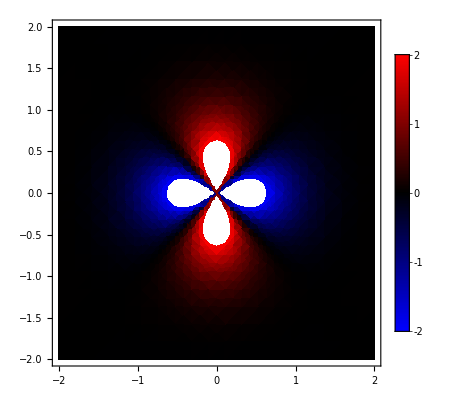

```mathematica
zP=Simplify[poynti[[3]]/.{Ah->0,Bh->0,Ae->1,Be->1,kz->1/2(2 π/λfree n1+2 π/λfree*n2)}];
zP=zP/.{λfree->1,n2->1,n1->1.1};
DensityPlot[Re[zP],{x,-2,2},{y,-2,2},PlotRange->{All,All,{-2,2}},PlotPoints->20,PlotLegends->Automatic,ColorFunction->cf]
```

## m != 0

### Cartesian Export

```mathematica
(*Note at the end all the fields should be multiplied by e^imϕ*)
ClearAll[γ, ω,ϵ1,ϵ0,λfree,n0,n1,a,s1,s0,n,m,n2];
reps={ω->(2π)/λfree};
er={1,0,0};
eϕ={0,1,0};
ez={0,0,1};

Ez1=Ae BesselJ[m,γ r];
Hz1=Ah BesselJ[m,γ r] ;
Ez2=Be BesselK[m,β r];
Hz2=Bh BesselK[m,β r] ;

Et1=I/γ^2(kz * ( D[Ez1,r]er + (I m)/r Ez1 eϕ)
-ω ( Cross[ez, ( D[Hz1,r]er + (I m)/r Hz1 eϕ)]) );
Et2=-I/β^2(kz * ( D[Ez2,r]er + (I m)/r Ez2 eϕ)
-ω ( Cross[ez, ( D[Hz2,r]er + (I m)/r Hz2 eϕ)]) );
Et1=Simplify[Et1,Assumptions->{ω>0,m>0}];
Et2=Simplify[Et2,Assumptions->{ω>0,m>0}];
Etρϕ1=Et1/.reps;
Etρϕ2=Et2/.reps;
Etρϕ1=Etρϕ1[[1;;2]];
Etρϕ2=Etρϕ2[[1;;2]];
(*Using the field in cylindrical components, find the field in cartesian coordinates*)
Et1xy=Etρϕ1[[1]]*{x/r,y/r}+Etρϕ1[[2]]*{-y/r,x/r};
Et1xy=Et1xy/.{r->√(x^2+y^2)};
Et2xy=Etρϕ2[[1]]*{x/r,y/r}+Etρϕ2[[2]]*{-y/r,x/r};
Et2xy=Et2xy/.{r->√(x^2+y^2)};
Et1xy=Et1xy/.reps;
Et2xy=Et2xy/.reps;
Et1xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Re[Et1xy]];
Et2xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Re[Et2xy]];

Ht1=I/γ^2(kz * ( D[Hz1,r]er + (I m)/r Hz1 eϕ)
+ω *n1^2( Cross[ez, ( D[Ez1,r]er + (I m)/r Ez1 eϕ)]) );
Ht2=-I/β^2(kz * ( D[Hz2,r]er + (I m)/r Hz2 eϕ)
+ω *n2^2( Cross[ez, ( D[Ez2,r]er + (I m)/r Ez2 eϕ)]) );

Ht1=Simplify[Ht1,Assumptions->{ω>0,m>0}];
Ht2=Simplify[Ht2,Assumptions->{ω>0,m>0}];

Htρϕ1=Ht1/.reps;
Htρϕ2=Ht2/.reps;
Htρϕ1=Htρϕ1[[1;;2]];
Htρϕ2=Htρϕ2[[1;;2]];

Ht1xy=Htρϕ1[[1]]*{x/r,y/r}+Htρϕ1[[2]]*{-y/r,x/r};
Ht1xy=Ht1xy/.{r->√(x^2+y^2)};
Ht2xy=Htρϕ2[[1]]*{x/r,y/r}+Htρϕ2[[2]]*{-y/r,x/r};
Ht2xy=Ht2xy/.{r->√(x^2+y^2)};

Ht1xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Ht1xy];

(*Tangential E and H are continous across interface*)
(* azimuthal dir *)
eq1=Simplify[(Et1/.{r->a})[[2]]==(Et2/.{r->a})[[2]]];
(* z dir *)
eq2=(Ez1/.{r->a})==(Ez2/.{r->a});
(* azimuthal dir *)
eq3=Simplify[(Ht1/.{r->a})[[2]]==(Ht2/.{r->a})[[2]]];
(* z dir *)
eq4=(Hz1/.{r->a})==(Hz2/.{r->a});

(*Normal D and B are continuous across boundary since B1 = μ1 H1, and B2 = μ2 * H2 and μ1=μ2 H normal is also continous across the boundary*)
eq5=Simplify[(n1^2*Et1/.{r->a})[[1]]==(n2^2*Et2/.{r->a})[[1]]];
eq6=Simplify[( Ht1/.{r->a})[[1]]==(Ht2/.{r->a})[[1]]];

{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.reps;
{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.{γ->√(n1^2 ω^2 -kz^2),β->√(kz^2-n2^2 ω^2)}/.{ω->(2π)/λfree};
(*{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.{ϕ->0};*)

eqns[kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[{eq1,eq2,eq3,eq4,eq5,eq6}];
```

```mathematica
(*When the eigenvalues for the secular equation are used, there are only three linearly independent equations. One may arbitrarily set Ae*)
soluAe={"Ae"->1,"Ah"->Ah,"Be"->Be,"Bh"->Bh}/.Solve[eqns[kz,{a,n2,n1,λfree,m}][[1;;3]]/.{Ae->1},{Ah,Be,Bh}][[1]];
soluAe=Simplify[soluAe];
soluAe=Association[soluAe];

funcTemplate=StringTemplate["def `coefficient`(a, n1, n2, λfree, m, kz):
    return `returnExpr`"];

funcStrings=Table[funcTemplate[<|"coefficient"->key, "returnExpr"->PythonForm[soluAe[key]]|>],{key,Keys[soluAe]}];
funcStrings=Riffle[funcStrings,"\n\n"];
funcString=StringJoin[funcStrings];
copyAsUnicode[funcString]
```

```mathematica
template=StringTemplate["def `fieldComponent`gen_1(Ae, Ah, Be, Bh, m, β, γ, kz, λfree):
    def `fieldComponent`(x,y):
        return ((np.cos(m*np.arctan2(y,x)) +  1j * np.sin(m*np.arctan2(y,x))) 
                * `fieldExpr`)
    return `fieldComponent`
"];

fieldExports=<|"Et1"->Et1xy,
"Et2"->Et2xy,
"Ht1"->Ht1xy,
"Ht2"->Ht2xy
|>;

axialFields="import numpy as np
from scipy import special

def Ezgen_1(Ae, m, γ):
    def Ez(ρ):
        return Ae * special.jv(m, ρ * γ)
    return Ez

def Ezgen_2(Be, m, β):
    def Ez(ρ):
        return Be * special.kn(m, ρ * β)
    return Ez

def Hzgen_1(Ah, m, γ):
    def Hz(ρ):
        return Ah * special.jv(m, ρ * γ)
    return Hz

def Hzgen_2(Bh, m, β):
    def Hz(ρ):
        return Bh * special.kn(m, ρ * β)
    return Hz

";

exportStrings=Table[template[<|"fieldComponent"->key,
"fieldExpr"->PythonForm[fieldExports[key]]|>],{key,Keys[fieldExports]}];
exportStrings=Riffle[exportStrings,"\n\n"];
exportString=axialFields<>StringJoin[exportStrings]<>"\n\n";

exportFname=FileNameJoin[{NotebookDirectory[],"fieldgen.py"}];
Export[exportFname,exportString,"Text"]
```

### Cylindrical Export

```mathematica
(*Note at the end all the fields should be multiplied by e^imϕ*)
ClearAll[γ, ω,ϵ1,ϵ0,λfree,n0,n1,a,s1,s0,n,m,n2];

reps={ω->(2π)/λfree};
eρ={1,0,0};
eϕ={0,1,0};
ez={0,0,1};

Ez1=Ae BesselJ[m,γ ρ];
Hz1=Ah BesselJ[m,γ ρ] ;
Ez2=Be BesselK[m,β ρ];
Hz2=Bh BesselK[m,β ρ] ;

Et1=I/γ^2(kz * ( D[Ez1,ρ]eρ + (I m)/ρ Ez1 eϕ)
-ω ( Cross[eρ, ( D[Hz1,ρ]eρ + (I m)/ρ Hz1 eϕ)]) );
Et2=-I/β^2(kz * ( D[Ez2,ρ]eρ + (I m)/ρ Ez2 eϕ)
-ω ( Cross[ez, ( D[Hz2,ρ]eρ + (I m)/ρ Hz2 eϕ)]) );
Et1=Simplify[Et1,Assumptions->{ω>0,m>0}];
Et2=Simplify[Et2,Assumptions->{ω>0,m>0}];
Etρϕ1=Et1/.reps;
Etρϕ2=Et2/.reps;
Etρϕ1=Etρϕ1[[1;;2]];
Etρϕ2=Etρϕ2[[1;;2]];
(*Using the field in cylindrical components, find the field in cartesian coordinates*)
Et1xy=Etρϕ1[[1]]*{x/ρ,y/ρ}+Etρϕ1[[2]]*{-y/ρ,x/ρ};
Et1xy=Et1xy/.{ρ->√(x^2+y^2)};
Et2xy=Etρϕ2[[1]]*{x/ρ,y/ρ}+Etρϕ2[[2]]*{-y/ρ,x/ρ};
Et2xy=Et2xy/.{ρ->√(x^2+y^2)};
Et1xy=Et1xy/.reps;
Et2xy=Et2xy/.reps;
Et1xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Re[Et1xy]];
Et2xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Re[Et2xy]];

Ht1=I/γ^2(kz * ( D[Hz1,ρ]eρ + (I m)/ρ Hz1 eϕ)
+ω *n1^2( Cross[ez, ( D[Ez1,ρ]eρ + (I m)/ρ Ez1 eϕ)]) );
Ht2=-I/β^2(kz * ( D[Hz2,ρ]eρ + (I m)/ρ Hz2 eϕ)
+ω *n2^2( Cross[ez, ( D[Ez2,ρ]eρ + (I m)/ρ Ez2 eϕ)]) );

Ht1=Simplify[Ht1,Assumptions->{ω>0,m>0}];
Ht2=Simplify[Ht2,Assumptions->{ω>0,m>0}];

Htρϕ1=Ht1/.reps;
Htρϕ2=Ht2/.reps;
Htρϕ1=Htρϕ1[[1;;2]];
Htρϕ2=Htρϕ2[[1;;2]];

Ht1xy=Htρϕ1[[1]]*{x/ρ,y/ρ}+Htρϕ1[[2]]*{-y/ρ,x/ρ};
Ht1xy=Ht1xy/.{ρ->√(x^2+y^2)};
Ht2xy=Htρϕ2[[1]]*{x/ρ,y/ρ}+Htρϕ2[[2]]*{-y/ρ,x/ρ};
Ht2xy=Ht2xy/.{ρ->√(x^2+y^2)};

Ht1xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Ht1xy];

(*Tangential E and H are continous across interface*)
(* azimuthal dir *)
eq1=Simplify[(Et1/.{ρ->a})[[2]]==(Et2/.{ρ->a})[[2]]];
(* z dir *)
eq2=(Ez1/.{ρ->a})==(Ez2/.{ρ->a});
(* azimuthal dir *)
eq3=Simplify[(Ht1/.{ρ->a})[[2]]==(Ht2/.{ρ->a})[[2]]];
(* z dir *)
eq4=(Hz1/.{ρ->a})==(Hz2/.{ρ->a});

(*Normal D and B are continuous across boundary since B1 = μ1 H1, and B2 = μ2 * H2 and μ1=μ2 H normal is also continous across the boundary*)
eq5=Simplify[(n1^2*Et1/.{ρ->a})[[1]]==(n2^2*Et2/.{ρ->a})[[1]]];
eq6=Simplify[( Ht1/.{ρ->a})[[1]]==(Ht2/.{ρ->a})[[1]]];

{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.reps;
(*{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.{γ->√(n1^2 ω^2 -kz^2),β->√(kz^2-n2^2 ω^2)}/.{ω->(2π)/λfree};*)
(*{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.{ϕ->0};*)
eqns[kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[{eq1,eq2,eq3,eq4,eq5,eq6}];
```

```mathematica
(*When the eigenvalues for the secular equation are used, there are only three linearly independent equations. One may arbitrarily set Ae*)
soluAe={"Ae"->1,"Ah"->Ah,"Be"->Be,"Bh"->Bh}/.Solve[eqns[kz,{a,n2,n1,λfree,m}][[1;;3]]/.{Ae->1},{Ah,Be,Bh}][[1]];
soluAe=Simplify[soluAe];
soluAe=Association[soluAe];

funcTemplate=StringTemplate["def `coefficient`(a, n1, n2, λfree, m, kz):
    return `returnExpr`"];

funcStrings=Table[funcTemplate[<|"coefficient"->key, "returnExpr"->PythonForm[soluAe[key]]|>],{key,Keys[soluAe]}];
funcStrings=Riffle[funcStrings,"\n\n"];
funcString=StringJoin[funcStrings];
copyAsUnicode[funcString]
```

```mathematica
template=StringTemplate["def `fieldComponent`genρ(Ae, Ah, Be, Bh, m, β, γ, kz, λfree, nCladding, nCore):
    def `fieldComponent`ρ(ρ):
        '''
        Returns the radial component of `fieldComponent` sans the global phase factor e(imϕ).
        Parameters
        ----------
        ρ : float
            The radial coordinate.
        Returns
        -------
        `fieldComponent`ρ : complex
        '''
        return `fieldExprρ`
    return `fieldComponent`ρ

def `fieldComponent`genϕ(Ae, Ah, Be, Bh, m, β, γ, kz, λfree, nCladding, nCore):
    def `fieldComponent`ϕ(ρ):
        '''
        Returns the azimuthal component of `fieldComponent` sans the global phase factor e(imϕ).
        Parameters
        ----------
        ρ : float
            The radial coordinate.
        Returns
        -------
        `fieldComponent`ϕ : complex
        '''
        return `fieldExprϕ`
    return `fieldComponent`ϕ
"];

fieldExports=<|"Et1"->Et1xy,
"Et2"->Et2xy,
"Ht1"->Ht1xy,
"Ht2"->Ht2xy
|>;
fieldExportsρ=<|
"Et1"->(Etρϕ1/.{r->ρ}),
"Et2"->(Etρϕ2/.{r->ρ}),
"Ht1"->(Htρϕ1/.{r->ρ}),
"Ht2"->(Htρϕ2/.{r->ρ})
|>;
axialFields="import numpy as np
from scipy import special

def Ezgen_1(Ae, m, γ):
    def Ez(ρ):
        return Ae * special.jv(m, ρ * γ)
    return Ez

def Ezgen_2(Be, m, β):
    def Ez(ρ):
        return Be * special.kn(m, ρ * β)
    return Ez

def Hzgen_1(Ah, m, γ):
    def Hz(ρ):
        return Ah * special.jv(m, ρ * γ)
    return Hz

def Hzgen_2(Bh, m, β):
    def Hz(ρ):
        return Bh * special.kn(m, ρ * β)
    return Hz

";

(*exportStrings=Table[template[<|
"fieldComponent"->key,
"fieldExprρ"->StringReplace[PythonForm[fieldExportsρ[key][[1]]],{"n1"->"nCore","n2"->"nCladding"}],
"fieldExprϕ"->StringReplace[PythonForm[fieldExportsρ[key][[2]]],{"n1"->"nCore","n2"->"nCladding"}],
|>],{key,Keys[fieldExportsρ]}];*)
exportStrings=Table[template[<|
"fieldComponent"->key,
"fieldExprρ"->StringReplace[PythonForm[fieldExportsρ[key][[1]]],{"n1"->"nCore","n2"->"nCladding"}],
"fieldExprϕ"->StringReplace[PythonForm[fieldExportsρ[key][[2]]],{"n1"->"nCore","n2"->"nCladding"}]
|>],{key,Keys[fieldExportsρ]}];
exportStrings=Riffle[exportStrings,"\n\n"];
exportString=axialFields<>StringJoin[exportStrings]<>"\n\n";

exportFname=FileNameJoin[{NotebookDirectory[],"fieldgen.py"}];
Export[exportFname,exportString,"Text"]
```

/Users/juan/ZiaLab/Codebase/wavesight/fieldgen.py

## m = 0

```mathematica
(*Note at the end all the fields should be multiplied by e^imϕ*)
ClearAll[γ, ω,ϵ1,ϵ0,λfree,n0,n1,a,s1,s0,n,m,n2,eqns];

reps={ω->(2π)/λfree,m->0};
er={1,0,0};
eϕ={0,1,0};
ez={0,0,1};

Ez1=Ae BesselJ[m,γ r];
Hz1=Ah BesselJ[m,γ r] ;
Ez2=Be BesselK[m,β r];
Hz2=Bh BesselK[m,β r] ;

Et1=I/γ^2(kz * ( D[Ez1,r]er + (I m)/r Ez1 eϕ)
-ω ( Cross[ez, ( D[Hz1,r]er + (I m)/r Hz1 eϕ)]) );
Et2=-I/β^2(kz * ( D[Ez2,r]er + (I m)/r Ez2 eϕ)
-ω ( Cross[ez, ( D[Hz2,r]er + (I m)/r Hz2 eϕ)]) );
Et1=Simplify[Et1,Assumptions->{ω>0,m>0}];
Et2=Simplify[Et2,Assumptions->{ω>0,m>0}];
Etρϕ1=Et1/.reps;
Etρϕ2=Et2/.reps;
Etρϕ1=Etρϕ1[[1;;2]];
Etρϕ2=Etρϕ2[[1;;2]];
(*Using the field in cylindrical components, find the field in cartesian coordinates*)
Et1xy=Etρϕ1[[1]]*{x/r,y/r}+Etρϕ1[[2]]*{-y/r,x/r};
Et1xy=Et1xy/.{r->√(x^2+y^2)};
Et2xy=Etρϕ2[[1]]*{x/r,y/r}+Etρϕ2[[2]]*{-y/r,x/r};
Et2xy=Et2xy/.{r->√(x^2+y^2)};
Et1xy=Et1xy/.reps;
Et2xy=Et2xy/.reps;
Et1xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Re[Et1xy]];
Et2xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Re[Et2xy]];

Ht1=I/γ^2(kz * ( D[Hz1,r]er + (I m)/r Hz1 eϕ)
+ω *n1^2( Cross[ez, ( D[Ez1,r]er + (I m)/r Ez1 eϕ)]) );
Ht2=-I/β^2(kz * ( D[Hz2,r]er + (I m)/r Hz2 eϕ)
+ω *n2^2( Cross[ez, ( D[Ez2,r]er + (I m)/r Ez2 eϕ)]) );

Ht1=Simplify[Ht1,Assumptions->{ω>0,m>0}];
Ht2=Simplify[Ht2,Assumptions->{ω>0,m>0}];

Htρϕ1=Ht1/.reps;
Htρϕ2=Ht2/.reps;
Htρϕ1=Htρϕ1[[1;;2]];
Htρϕ2=Htρϕ2[[1;;2]];

Ht1xy=Htρϕ1[[1]]*{x/r,y/r}+Htρϕ1[[2]]*{-y/r,x/r};
Ht1xy=Ht1xy/.{r->√(x^2+y^2)};
Ht2xy=Htρϕ2[[1]]*{x/r,y/r}+Htρϕ2[[2]]*{-y/r,x/r};
Ht2xy=Ht2xy/.{r->√(x^2+y^2)};

Ht1xyField[x_,y_,kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[Ht1xy];

(*Tangential E and H are continous across interface*)
(* azimuthal dir *)
eq1=Simplify[(Et1/.{r->a})[[2]]==(Et2/.{r->a})[[2]]];
(* z dir *)
eq2=(Ez1/.{r->a})==(Ez2/.{r->a});
(* azimuthal dir *)
eq3=Simplify[(Ht1/.{r->a})[[2]]==(Ht2/.{r->a})[[2]]];
(* z dir *)
eq4=(Hz1/.{r->a})==(Hz2/.{r->a});

(*Normal D and B are continuous across boundary since B1 = μ1 H1, and B2 = μ2 * H2 and μ1=μ2 H normal is also continous across the boundary*)
eq5=Simplify[(n1^2*Et1/.{r->a})[[1]]==(n2^2*Et2/.{r->a})[[1]]];
eq6=Simplify[( Ht1/.{r->a})[[1]]==(Ht2/.{r->a})[[1]]];

{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.reps;
{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.{γ->√(n1^2 ω^2 -kz^2),β->√(kz^2-n2^2 ω^2)}/.{ω->(2π)/λfree};
(*{eq1,eq2,eq3,eq4,eq5,eq6} = {eq1,eq2,eq3,eq4,eq5,eq6}/.{ϕ->0};*)

eqns[kz_,{a_,n2_,n1_,λfree_,m_}]:=Evaluate[{eq1,eq2,eq3,eq4,eq5,eq6}];
```

```mathematica
soluAe2={"Ah"->0,"Ae"->1,"Be"->Be,"Bh"->0}/.Solve[Pick[eqns[kz,{a,n2,n1,λfree,m}],{False,True,False,False,False,False}]/.{Ae->1},{Be}][[1]]
```

{Ah→0,Ae→1,Be→BesselJ[0,a √(-kz^2+(4 n1^2 π^2)/λfree^2)]/BesselK[0,a √(kz^2-(4 n2^2 π^2)/λfree^2)],Bh→0}

```mathematica
(*When the eigenvalues for the secular equation are used, there are only three linearly independent equations. One may arbitrarily set Ae*)
soluAh={"AhTM"->1,"AeTM"->Ae,"BeTM"->Be,"BhTM"->Bh}/.Solve[eqns[kz,{a,n2,n1,λfree,m}][[1;;3]]/.{Ah->1},{Ae,Be,Bh}][[1]];
soluAh=Simplify[soluAh];
soluAh=Association[soluAh];

funcTemplate=StringTemplate["def `coefficient`(a, n1, n2, λfree, kz):
    return `returnExpr`"];

funcStrings=Table[funcTemplate[<|"coefficient"->key, "returnExpr"->PythonForm[soluAh[key]]|>],{key,Keys[soluAh]}];
funcStrings=Riffle[funcStrings,"\n\n"];
funcString=StringJoin[funcStrings];
copyAsUnicode[funcString]
```

```mathematica
soluAe2={"AhTE"->0,"AeTE"->1,"BeTE"->Be,"BhTE"->0}/.Solve[Pick[eqns[kz,{a,n2,n1,λfree,m}],{False,True,False,False,False,False}]/.{Ae->1},{Be}][[1]];
soluAe2=Simplify[soluAe2];
soluAe2=Association[soluAe2];

funcTemplate=StringTemplate["def `coefficient`(a, n1, n2, λfree, kz):
    return `returnExpr`"];

funcStrings=Table[funcTemplate[<|"coefficient"->key, "returnExpr"->PythonForm[soluAe2[key]]|>],{key,Keys[soluAe2]}];
funcStrings=Riffle[funcStrings,"\n\n"];
funcString=StringJoin[funcStrings];
copyAsUnicode[funcString]
```

```mathematica
template=StringTemplate["def `fieldComponent`gen_1m0(Ae, Ah, Be, Bh, β, γ, kz, λfree):
    def `fieldComponent`(x,y):
        return `fieldExpr`
    return `fieldComponent`
"];

fieldExports=<|"Et1"->Et1xy,
"Et2"->Et2xy,
"Ht1"->Ht1xy,
"Ht2"->Ht2xy
|>;

axialFields="import numpy as np
from scipy import special

def Ezgen_1m0(Ae, γ):
    def Ez(ρ):
        return Ae * special.jv(0, ρ * γ)
    return Ez

def Ezgen_2m0(Be, β):
    def Ez(ρ):
        return Be * special.kn(0, ρ * β)
    return Ez

def Hzgen_1m0(Ah, γ):
    def Hz(ρ):
        return Ah * special.jv(0, ρ * γ)
    return Hz

def Hzgen_2m0(Bh, β):
    def Hz(ρ):
        return Bh * special.kn(0, ρ * β)
    return Hz

";

exportStrings=Table[template[<|"fieldComponent"->key,
"fieldExpr"->PythonForm[fieldExports[key]]|>],{key,Keys[fieldExports]}];
exportStrings=Riffle[exportStrings,"\n\n"];
exportString=axialFields<>StringJoin[exportStrings]<>"\n\n";

exportFname=FileNameJoin[{NotebookDirectory[],"fieldgenTETM.py"}];
(*Export[exportFname,exportString,"Text"]*)
```

/Users/juan/ZiaLab/Codebase/wavesight/fieldgenTETM.py

## Gray' s Notation (DEPRECATED)

from AIP Handbook of Physics 1979

-Graphics-

```mathematica
D[BesselJ[m,x],x]
D[BesselK[m,x],x]
```

1/2 (BesselJ[-1+m,x]-BesselJ[1+m,x])

1/2 (-BesselK[-1+m,x]-BesselK[1+m,x])

```mathematica
(*How many terms and whether to use the polynomial expression for ratios of BesselK*)
besselRatioTerms=50;
besselApprox=False;
(*Whether to use the alternate form*)
useAlternateForm=False;
ClearAll[γ, ω,ϵ1,ϵ0,λfree,n0,n1,a,s1,s0,n];
reps={ϵ1-> n1^2,ϵ0->n0^2,s1->√(ω^2 n1^2-γ^2),s0->√(γ^2-ω^2 n0^2)}/.{ω->(2π)/λfree};
tm=ϵ1/(2ϵ0 s1 a)(BesselJ[n-1,s1 a]-BesselJ[n+1,s1 a])/BesselJ[n,s1 a]+1/(2s0 a)*(-BesselK[-1+n,s0 a]-BesselK[1+n,s0 a])/BesselK[n,s0 a];
(*this equivalent version is more numerically stable*)
If[useAlternateForm,
tm=ϵ1/(2ϵ0 s1 a)(BesselJ[n-1,s1 a]-BesselJ[n+1,s1 a])+1/(2s0 a)*(-BesselK[-1+n,s0 a]-BesselK[1+n,s0 a])/BesselK[n,s0 a]*BesselJ[n,s1 a]];
If[besselApprox,
tm=tm/.{BesselK[α_,z_]->BesselKPoly[besselRatioTerms,α,z]}
];
te=1/(s1 a)(1/2 (BesselJ[-1+n,s1 a]-BesselJ[1+n,s1 a]))/BesselJ[n,s1 a]+1/(s0 a)*(1/2 (-BesselK[-1+n,s0 a]-BesselK[1+n,s0 a]))/BesselK[n,s0 a];
(*this equivalent version is more numerically stable*)
If[besselApprox,
te=1/(s1 a)1/2 (BesselJ[-1+n,s1 a]-BesselJ[1+n,s1 a])+1/(s0 a)*(1/2 (-BesselK[-1+n,s0 a]-BesselK[1+n,s0 a]))/BesselK[n,s0 a]*BesselJ[n,s1 a]];
(*There are ration of BesselK that are ratios of two very small quantities, however most of that is a common exponential that cancels out, leaving a simpler expression*)
If[besselApprox,
te=te/.{BesselK[α_,z_]->BesselKPoly[besselRatioTerms,α,z]}];
he=(n^2/a^2*(1/(s0^2 a^2)+ϵ1/ϵ0*1/(s1^2 a^2))*(1/s0^2+1/s1^2));
(*this equivalent version is more numerically stable*)
If[useAlternateForm,
he=(n^2/a^2*(1/(s0^2 a^2)+ϵ1/ϵ0*1/(s1^2 a^2))*(1/s0^2+1/s1^2))*BesselJ[n,s1 a]^2];
tm=tm/.reps;
te=te/.reps;
he=he/.reps;
tmte=tm*te;
he=tmte-he;
TM[γ_,{a_,n0_,n1_,λfree_,n_}]:=Evaluate[tm];
TE[γ_,{a_,n0_,n1_,λfree_,n_}]:=Evaluate[te];
HE[γ_,{a_,n0_,n1_,λfree_,n_}]:=Evaluate[he];
fiberFuncs=<|"TM"->TM,"TE"->TE,"HE"->HE|>;
```

```mathematica
fortranTM=PythonForm[tm]
copyAsUnicode[ToString[fortranTM]]
```

(n1**2*(special.jv(-1 + n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)) - special.jv(1 + n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2))))/(2.*a*n0**2*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)*special.jv(n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2))) + (-special.kn(-1 + n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)) - special.kn(1 + n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)))/(2.*a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)*special.kn(n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)))

```mathematica
fortranTE=PythonForm[te]
copyAsUnicode[ToString[fortranTE]]
```

(special.jv(-1 + n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)) - special.jv(1 + n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)))/(2.*a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)*special.jv(n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2))) + (-special.kn(-1 + n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)) - special.kn(1 + n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)))/(2.*a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)*special.kn(n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)))

```mathematica
fortranHE=PythonForm[he]
copyAsUnicode[ToString[fortranHE]]
```

-((n**2*(1/(γ**2 - (4*n0**2*np.pi**2)/λfree**2) + 1/(-γ**2 + (4*n1**2*np.pi**2)/λfree**2))*(1/(a**2*(γ**2 - (4*n0**2*np.pi**2)/λfree**2)) + n1**2/(a**2*n0**2*(-γ**2 + (4*n1**2*np.pi**2)/λfree**2))))/a**2) + ((special.jv(-1 + n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)) - special.jv(1 + n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)))/(2.*a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)*special.jv(n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2))) + (-special.kn(-1 + n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)) - special.kn(1 + n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)))/(2.*a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)*special.kn(n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2))))*((n1**2*(special.jv(-1 + n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)) - special.jv(1 + n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2))))/(2.*a*n0**2*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2)*special.jv(n,a*np.sqrt(-γ**2 + (4*n1**2*np.pi**2)/λfree**2))) + (-special.kn(-1 + n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)) - special.kn(1 + n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)))/(2.*a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2)*special.kn(n,a*np.sqrt(γ**2 - (4*n0**2*np.pi**2)/λfree**2))))